```mathematica
afile[am_]:=afileDir[am]<>"txt_stack/rods.txt";
rods[am_]:=ReadList[afile[am],Number,RecordLists->True];
angles[rods_]:=Table[ArcTan[rods[[i,3]],rods[[i,4]]],{i,1,Length[rods]}];
```

## Controls

```mathematica
nT = 1000;
nRod=1;
nFil=100;
Subscript[ρ, pm]=0.5;
Δx=50;
Δy=50;
nPm=Round[Subscript[ρ, pm]*Δx*Δy];
nAm[am_]:=Round[ToExpression[am]Δx Δy]
afileDir[am_] := "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/clnks_amRho"<>am<>"/";
ams={".05"};
```

Idea: Measure correlation of displacements as a function of distance
Define: displacement dr_(m,i) = r_(m,i+1)-r_(m,i) 
where i represents time
and r_m is the center of mass position of rod m 
Define: 
Corr[r_(m,i), r_(n,i)]=dr_(m,i)· dr_(n,i)
Dist[r_(m,i), r_(n,i)]=|r_(m,i)-r_(n,i)|

Create a table of {Corr[r_(m,i), r_(n,i)],Dist[r_(m,i), r_(n,i)]} for every set of rods, 

Bin by distance.

```mathematica
r=rods[".02"];
```

```mathematica
rt=Partition[r,Length[r]/nT];
```

```mathematica
corrs=Table[
{
EuclideanDistance[
{rt[[t,i,1]],rt[[t,i,2]]},
{rt[[t,j,1]],rt[[t,j,2]]}
],
Correlation[
{rt[[t+50,i,1]]-rt[[t,i,1]],rt[[t+50,i,2]]-rt[[t,i,2]]},
{rt[[t+50,j,1]]-rt[[t,j,1]],rt[[t+50,j,2]]-rt[[t,j,2]]}
]
},
{t,Round[Length[rt]/2],Length[rt]-50,50},
{i,1,Length[rt[[t]]]},
{j,i,Length[rt[[t]]]}
];
```

```mathematica
sortedCorrs=Sort[Flatten[corrs,2]];
binnedCorrs[binSize_]:=
Table[Mean[sortedCorrs[[i;;i+binSize]]],{i,1,Length[sortedCorrs]-binSize,binSize}];
```

```mathematica
Length[allCorrs]
```

50500

```mathematica
allCorrsSorted=Sort[allCorrs];
```

```mathematica
t=Table[Mean[allCorrsSorted[[i;;i+100]]],{i,1,Length[allCorrsSorted]-100,100}];
```

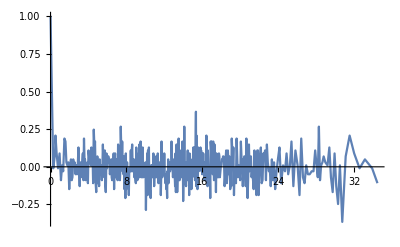

```mathematica
ListLinePlot[t,PlotRange->All]
```